## Física Computacional III Prueba 3 6/6/2019

## Problema 2

Confirme, usando NBodySimulation,que las distancias y fechas de la figura son aproximadamente correctas. 
Hint: El comando Peaks le puede ser útil
-Graphics-

```mathematica
sol=Entity["Star","Sun"]
```

Sun

```mathematica
tierra=Entity["Planet","Earth"]
```

Earth

```mathematica
marte=Entity["Planet","Mars"]
```

Mars

```mathematica
date=DateObject[{2016, 1, 1}]
```

Day: Fri 1 Jan 2016

```mathematica
solPos = Table[Quantity[0,"AstronomicalUnits"],3];
tierraPos= EntityValue[tierra, EntityProperty["Planet","HelioCoordinates",{"Date"->date}]];
martePos = EntityValue[marte, EntityProperty["Planet","HelioCoordinates",{"Date"->date}]];
```

```mathematica
dia=Quantity[1,"day"];
```

```mathematica
solVel=solPos/dia;
tierraVel= (EntityValue[tierra, EntityProperty["Planet","HelioCoordinates",{"Date"->date+dia}]]-tierraPos)/dia;
marteVel = (EntityValue[marte, EntityProperty["Planet","HelioCoordinates",{"Date"->date+dia}]]-martePos)/dia;
```

```mathematica
data = NBodySimulation["Newtonian",<|sol-><|"Position"->solPos,  "Velocity"->solVel|>,tierra-><|"Position"->tierraPos, "Velocity"->tierraVel|>, marte-><|"Position"->martePos,"Velocity"->marteVel|>|>, Quantity[20, "Years"]]
```

NBodySimulationData[…]

```mathematica
tend=data["SimulationTime"]; (*tiempo final*)
```

```mathematica
Show[ParametricPlot3D[Evaluate[data[tierra,"Position",t]],{t,0,tend}],ParametricPlot3D[Evaluate[data[marte,"Position",t]],{t,0,tend}],Graphics3D@Point[{0,0,0}]] (*ahora un parametric plot para observar lo que se hizo*)
```

-Graphics3D-

```mathematica
semana=UnitConvert[Quantity[7,"Days"],"Seconds"][[1]] (*Convertimos una semana en segundos, y eso es lo que avanzaremos como dt; tambien [[1]]] es para tomar unicamente la magnitud*)
```

604800

```mathematica
datpos=Table[{t,Evaluate[Norm[data[marte,"Position",t]-data[tierra,"Position",t]]]},{t,0,tend,semana}];  (*Entrega una lista con los tiempos y las distancias entre marte y al tierra*)
```

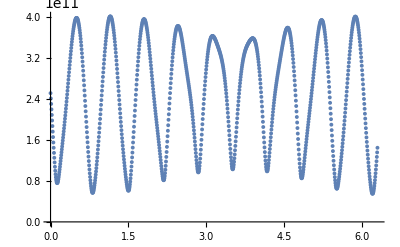

```mathematica
ListLinePlot[datpos,Joined->False] (*He aqui visualizada*)
```

```mathematica
datpos
```

datpos

```mathematica
pos=FindPeaks[-datpos[[All,2]]][[All,1]] (*nos entrega el numero de dato que posee un peak*)
```

{22,135,249,362,472,582,691,801,913,1027}

```mathematica
dmins=Table[datpos[[k]],{k,pos}]
```

{{12700800,7.57644×10^10},{81043200,5.68039×10^10},{149990400,6.10153×10^10},{218332800,8.14936×10^10},{284860800,9.6784×10^10},{351388800,1.02852×10^11},{417312000,9.88471×10^10},{483840000,8.53732×10^10},{551577600,6.49763×10^10},{620524800,5.50411×10^10}}

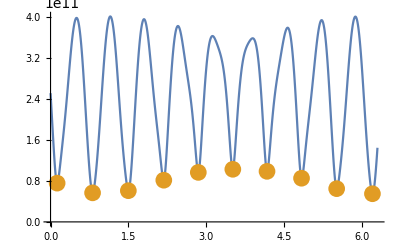

```mathematica
ListLinePlot[{datpos,dmins},Joined->{True,False},PlotStyle->{Automatic,PointSize[.03]}]
```

```mathematica
años=UnitConvert[Quantity[#,"Seconds"],"Years"]&/@dmins[[All,1]]
```

{147/365 yr,938/365 yr,1736/365 yr,2527/365 yr,3297/365 yr,4067/365 yr,966/73 yr,1120/73 yr,6384/365 yr,7182/365 yr}

```mathematica
agnos=años[[All,1]]//N
```

{0.40274,2.56986,4.75616,6.92329,9.03288,11.1425,13.2329,15.3425,17.4904,19.6767}

```mathematica
{agnos+2016,dmins[[All,2]]/10^9}ᵀ//TableForm
```

2016.4 | 75.7644
2018.57 | 56.8039
2020.76 | 61.0153
2022.92 | 81.4936
2025.03 | 96.784
2027.14 | 102.852
2029.23 | 98.8471
2031.34 | 85.3732
2033.49 | 64.9763
2035.68 | 55.0411

## Problema 3

## Un disco, que gira con velocidad angular ω constante, tiene un agujero a una distancia d del centro. Desde un punto fijo, ubicado inmediatamente bajo el disco, se lanza una particula que atraviesa por el agujero. Considerando que hay roce con el aire y que su modulo es proporcional al cuadrado de la magnitud de la velocidad (V), es decir, f_roce= - γ V^2. Calcule las condiciones iniciales V_0 y α (ver figura), que debe tener la particula, para que al caer, vuelva a cruzar por el (unico) agujero, situado ahora en un punto diametralmente opuesto al del lanzamiento. ¿Cuanto tiempo demora el vuelo? -Graphics- Datos: Utilice valores razonables para ω y d. Use un solo valor de γ tal que: 0<γ<1.

```mathematica
g=-9.8;
```

```mathematica
ecu={x''[t]==-.5v0^2 Cos[α],y''[t]==g-.5 v0^2 Sin[α]};
```

```mathematica
con={x'[t]==v0 Cos[α],y'[t]==v0 Sin[α],x[0]==0,y[0]==0};
```